## Plate Equation

The simplest version of a plate equation for the mid-plane displacement w of a flat plate (equilibrium, isotropic, uniform-…) under a transverse load f_1 is
	k Δ^2 w= k Δ(Δw) =Δ(k Δw)= f_1
The equation for the transverse displacement u of a membrane under a transverse load f_2 is
	TΔu=f_2
I can assemble a drum by pasting the two together with very stiff springs and making the stiffness k very small where there is no frame.

Boundary conditions are complicated for the plate equation.  We are just going to use all natural boundary conditions.

## First Two Coupled Laplacians

```mathematica
{R1,R2}={23.0,18.5}/2;
{T,k,Stiff}={1,1,10^2};
Ω=Disk[{0,0},R1];
{λ,UV}=NDEigensystem[{
-Laplacian[u[x,y],{x,y}]+Stiff(u[x,y]-v[x,y]), 
-Laplacian[v[x,y],{x,y}]-Stiff (u[x,y]-v[x,y]),
DirichletCondition[u[x,y]==0,True]
},{u,v},{x,y}∈Ω,6];
```

```mathematica
i=4;
{uSol,vSol}=UV⟦i⟧;
Plot3D[{uSol[x,y],vSol[x,y]},{x,y}∈Ω]
```

-Graphics3D-

## Next a Biharmonic

Houston we have a problem.

```mathematica
{R1,R2}={23.0,18.5}/2;
{T,k,Stiff}={1,1,10^2};
Ω=Disk[{0,0},R1];
{λ,W}=NDEigensystem[{
-Laplacian[Laplacian[w[x,y],{x,y}],{x,y}]
},w,{x,y}∈Ω,6];
```

NDEigensystem::femcmsd: The spatial derivative order of the PDE may not exceed two.

Set::shape: Lists {λ,W} and NDEigensystem[{-w^(0,4)[x,y]-2 w^(2,2)[x,y]-w^(4,0)[x,y]},w,{x,y}∈Disk[{0,0},11.5],6] are not the same shape.

Lots of FE tools do not like higher order equations.  There is a standard trick!

```mathematica
{R1,R2}={23.0,18.5}/2;
{T,k,Stiff}={1,1,10^2};
Ω=Disk[{0,0},R1];
{λ,W}=NDEigensystem[{
Laplacian[w[x,y],{x,y}]-wp[x,y],
Laplacian[wp[x,y],{x,y}],
DirichletCondition[w[x,y]==0,True]
},{w,wp},{x,y}∈Ω,12];
λ
```

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{0,19,«2008»,22128},{«1»}},{0.215884,-0.0115908,-0.0100166,-0.00939201,-0.00816966,-0.00717438,«22116»,1.82146×10^-17,0.0729444,0.0552455,0.0552455,0.0729444,0.25638}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

{-6.27395×10^-17,-0.0256297,-0.0256357,-0.0437428,-0.0705405-7.79204×10^-6 ⅈ,-0.0705405+7.79204×10^-6 ⅈ,-0.110914,-0.111082,-0.11135,-0.133421,-0.133507,-0.199444}

```mathematica
i=7;
{wSol,wpSol}=W⟦i⟧;
Plot3D[{wSol[x,y],wpSol[x,y]},{x,y}∈Ω,
PlotLegends->{"w","wp"},
PlotRange->All]
```

-Graphics3D-

I am taking the warning seriously and here is the computation using a different eigensolver.  It is way slower!

```mathematica
{R1,R2}={23.0,18.5}/2;
{T,k,Stiff}={1,1,10^2};
Ω=Disk[{0,0},R1];
{λ,W}=NDEigensystem[{
Laplacian[w[x,y],{x,y}]-wp[x,y],
Laplacian[wp[x,y],{x,y}],
DirichletCondition[wp[x,y]==0,True]
},{w,wp},{x,y}∈Ω,12,
Method->{"Eigensystem"->"Direct"}];
λ
```

{0.,-0.025633,-0.025633,-0.0437295,-0.0705373,-0.0705374,-0.111022,-0.111022,-0.111022,-0.133469,-0.13347,-0.199459}

```mathematica
i=11;
{wSol,wpSol}=W⟦i⟧;
Plot3D[{wSol[x,y],wpSol[x,y]},{x,y}∈Ω,
PlotLegends->{"w","wp"},
PlotRange->All]
```

-Graphics3D-

## Third a Coupled Laplacian Biharmonic

```mathematica
{R1,R2}={23.0,18.5}/2;
{T,k,Stiff}={1,1,10^2};
Ω=Disk[{0,0},R1];
{λ,UWWp}=NDEigensystem[{
-Laplacian[u[x,y],{x,y}]+Stiff(u[x,y]-wp[x,y]), 
k*Laplacian[w[x,y],{x,y}]-wp[x,y],
Laplacian[wp[x,y],{x,y}]-Stiff(u[x,y]-wp[x,y]),
DirichletCondition[wp[x,y]==0,True],
DirichletCondition[u[x,y]==0,True]
},{u,w,wp},{x,y}∈Ω,12]
```

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{0,19,«2965»,32517},{«1»}},{0.215884,-0.0115908,-0.0100166,-0.00939201,-0.00816966,-0.00717438,«32505»,1.82146×10^-17,0.0729444,0.0552455,0.0552455,0.0729444,0.25638}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

{{-7.29071×10^-13,-9.55571×10^-6,-0.0000610824,-0.0000626813,-0.000197588,-0.00019962,-0.000266987,-0.000476614-1.20946×10^-6 ⅈ,-0.000476614+1.20946×10^-6 ⅈ,-0.000682955,-0.000707807,-0.000944664},{{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}}

```mathematica
i=10;
{uSol,wSol,wpSol}=UWWp⟦i⟧;
Plot3D[{uSol[x,y],wSol[x,y]},{x,y}∈Ω,
PlotRange->All,
PlotLegends->{"u","w"}]
```

-Graphics3D-

## Fourth a Coupled Laplacian Biharmonic With the biharmonic off in the interior

```mathematica
{R1,R2}={23.0,18.5}/2;
{T,k,Stiff}={1,1,100};
SwitchFun[r_]:= If[r<R2,0.000001,1]
Ω=Disk[{0,0},R1];
{λ,UWWp}=NDEigensystem[{
-Laplacian[u[x,y],{x,y}]+Stiff(u[x,y]-wp[x,y]), 
Laplacian[w[x,y],{x,y}]-wp[x,y],
k*SwitchFun[√(x^2+y^2)]*Laplacian[wp[x,y],{x,y}]-Stiff(u[x,y]-wp[x,y]),
DirichletCondition[wp[x,y]==0,True],
DirichletCondition[u[x,y]==0,True]
},{u,w,wp},{x,y}∈Ω,12];
λ
```

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{0,«2754»,28077},«1»},{0.143232,-0.00814742,-0.00743605,-0.014424,-1.24033×10^-16,-0.00034126,«28065»,-1.73472×10^-18,0.0863047,0.0863047,0.0597178,0.0597178,0.292045}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

{-7.64972×10^-17,-0.018608,-0.0187767,-0.018819,-0.0193539,-0.0193669,-0.0202927,-0.0203392,-0.0216541,-0.0217397,-0.0235052,-0.0235814}

```mathematica
i=2;
{uSol,wSol,wpSol}=UWWp⟦i⟧;
Plot3D[{uSol[x,y],wSol[x,y]},{x,y}∈Ω,
PlotRange->All,
PlotLegends->{"u","w"}]
```

-Graphics3D-

# Mathematica PDE test.

I want to see if Mathematica can do our drums.  I woke up this morning and thought it might just work! I am going to do the circular drum

```mathematica
{R1,R2}={18.5,23.0}/2;
frameBase=RegionDifference[ Disk[{0,0},R2],Disk[{-0,0},R1]]
NDEigensystem[
{Laplacian[Laplacian[u[x,y],{x,y}],{x,y}]},
u,{x,y}∈frameBase,3]
```

BooleanRegion[#1&&!#2&,{Disk[{0,0},11.5],Disk[{0,0},9.25]}]

NDEigensystem::femcmsd: The spatial derivative order of the PDE may not exceed two.

NDEigensystem[{u^(0,4)[x,y]+2 u^(2,2)[x,y]+u^(4,0)[x,y]},u,{x,y}∈BooleanRegion[#1&&!#2&,{Disk[{0,0},11.5],Disk[{0,0},9.25]}],3]

```mathematica
λs/λs[[2]]
```

{2.17655×10^-11,1.,1.,15.3414,15.3414,72.7269,72.7275,211.818,211.826,473.366,473.376,489.683}

```mathematica
{-2.6240936430185307*^-12,0.9999999999999999,1.0000011922782532,15.972730905513476,15.972815179226298,80.36069485227416,80.36074268875335,250.09449322179796,250.10221330522575,592.6788236075297,592.7214581699053,1171.4939099649114}
```

```mathematica
{λs,UVs}=NDEigensystem[
{Laplacian[v[x,y],{x,y}]-u[x,y],
Laplacian[u[x,y],{x,y}]
},
{u,v},{x,y}∈frameBase,15]
```

{{-2.28221×10^-16,0.0000869712,0.0000869713,0.00138917,0.00138918,0.00698907,0.00698907,0.021751,0.0217517,0.051546,0.0515497,0.101886,0.101905,0.176581,0.176615},{{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]}}}

```mathematica
?Disk
```

## Frame

In need to define a  frame!  The fancy way did not work so here is an old fashioned way

```mathematica
{R1,R2,h}={11.2,12.3,0.1};
frameRegion=Region[ImplicitRegion[{-h<z<h, R1^2<x^2+y^2<R2^2},{x,y,z}]]
```

-Graphics3D-

### Laplacian Coordinates

Lets see if we can manage to do the Laplacian on the frame in Cylindrical coordinates.

```mathematica
{R1,R2,h}={11.2,12.3,0.1};
{{λ1,λ2,λ3},{v1,v2,v3}}=NDEigensystem[
{-Laplacian[u[x,y,z],{x,y,z}],
DirichletCondition[u[x,y,z]==0,True]
},
u,{x,y,z}∈frameRegion,3]
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[<4077597>, {233283, 233283}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

{{259.663,259.814,260.176},{InterpolatingFunction[{{-12.3, 12.3}, {-12.3, 12.3}, {-0.1, 0.1}}, <>],InterpolatingFunction[{{-12.3, 12.3}, {-12.3, 12.3}, {-0.1, 0.1}}, <>],InterpolatingFunction[{{-12.3, 12.3}, {-12.3, 12.3}, {-0.1, 0.1}}, <>]}}

```mathematica
ParametricPlot3D[ {r Cos[θ], r Sin[θ],v2[r Cos[θ],r Sin[θ],0]},{r,R1,R2},{θ,0.001, 2π},
PlotRange->All]
```

-Graphics3D-

## Geometry

In need the frame and the membrane.  I am going to do the circular drum!

```mathematica
{R1,R2,h}={2.3,2.4,0.1};
DiscretizeRegion[
RegionUnion[
ParametricRegion[{r Cos[θ], r Sin[θ],0},{{θ,0,2π}, {r,0,R2}}],
ParametricRegion[{r Cos[θ], r Sin[θ],z},{{θ,0,2π}, {r,R1,R2},{z,-h,h}}]
]]
```

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region BooleanRegion[«2»].

DiscretizeRegion[BooleanRegion[#1||#2&,{ParametricRegion[{{Cos[θ] r,r Sin[θ],0},0≤θ≤2 π&&0≤r≤2.4},{θ,r}],ParametricRegion[{{Cos[θ] r,r Sin[θ],z},0≤θ≤2 π&&2.3≤r≤2.4&&-0.1≤z≤0.1},{θ,r,z}]}]]

```mathematica
ImplicitRegion[{
```

```mathematica
Disk
```

```mathematica
Graphics3D[Cylinder[{{0,0,0},{0,0,0.00001}},R1]]
```

-Graphics3D-

```mathematica
{R1,R2,h}={12.1,11.2,0.2};
MeshRegion[Cylinder[{{0,0,-h},{0,0,h}},R1]]
drumFrame=RegionUnion[
RegionDifference[ 
Cylinder[{{0,0,-h},{0,0,h}},R1],
Cylinder[{{0,0,-h},{0,0,h}},R2]],
Cylinder[{{0,0,0},{0,0,0}},R2]]
MeshRegion[drumFrame]
```

MeshRegion[Cylinder[{{0,0,-0.2},{0,0,0.2}},12.1]]

BooleanRegion[(#1&&!#2)||#3&,{Cylinder[{{0,0,-0.2},{0,0,0.2}},12.1],Cylinder[{{0,0,-0.2},{0,0,0.2}},11.2],Cylinder[{{0,0,0},{0,0,0}},11.2]}]

MeshRegion[BooleanRegion[(#1&&!#2)||#3&,{Cylinder[{{0,0,-0.2},{0,0,0.2}},12.1],Cylinder[{{0,0,-0.2},{0,0,0.2}},11.2],Cylinder[{{0,0,0},{0,0,0}},11.2]}]]

## Linear Elasticity

## The circle is easy!

Defined entirely by the radius R

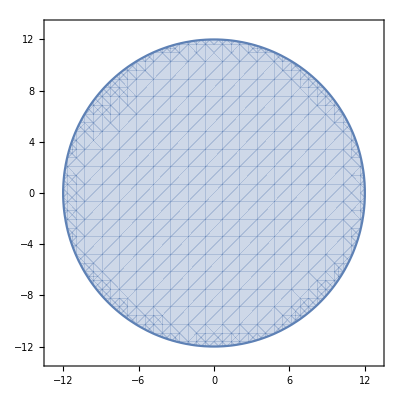

```mathematica
R=12;
RegionPlot[ x^2+y^2≤R^2,{x, -13,13},{y,-13,13}]
```

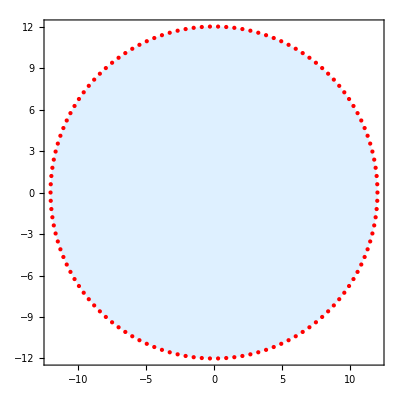

```mathematica
R=12.0; n=126;
BorderPoints=Table[R{Cos[θ],Sin[θ]},{θ,2π/n, 2π, 2π/n}];
Graphics[{{LightBlue,Polygon[BorderPoints]},{Red, Point[BorderPoints]}},Frame->True]
```

## The Square and Rectangle Can be done together!

Defined by the two side lengths 2a and 2b along with the rounded of radius r.  The center of each rounding off circle is displaced {r,r} towards the inside of the rectangle from the corner.

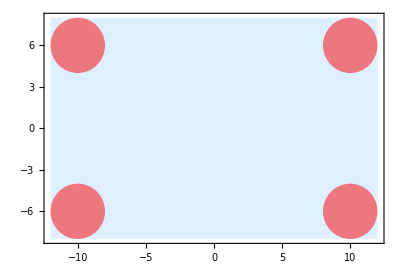

```mathematica
{a,b,r}={12.0,8.0,2.0};
Graphics[{
{LightBlue,Rectangle[{-a,-b},{a,b}]},
{Opacity[0.5], Red,
Disk[{a-r,b-r},r],
Disk[{-a+r,b-r},r],
Disk[{-a+r,-b+r},r],
Disk[{a-r,-b+r},r]}},Frame->True]
```

We can make the rounded off rectangle we want by putting edges together.  All I really need are dots around the outside of each quarter circle in the correct ccw order!  Lets think about it for a second.

{a,b}  we need 0≤θ≤π/2.

{-a,b}  we need π/2≤θ≤π.

{-a,-b}  we need π≤θ≤3π/2.

{a,-b}  we need 3π/2≤θ≤2π.

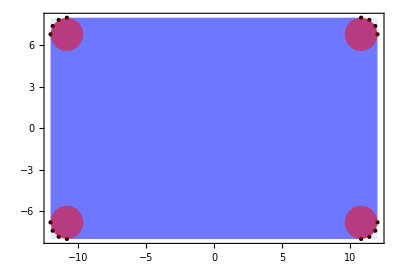

```mathematica
n=6;
BorderPoints=Join[
Table[{a-r,b-r}+r {Cos[θ],Sin[θ]},{θ,0,π/2,π/n}],
Table[{-a+r,b-r}+r {Cos[θ],Sin[θ]},{θ,π/2,π,π/n}],
Table[{-a+r,-b+r}+r {Cos[θ],Sin[θ]},{θ,π,3π/2,π/n}],
Table[{a-r,-b+r}+r {Cos[θ],Sin[θ]},{θ,3π/2,2π,π/n}]];
Graphics[{
{LightBlue,Rectangle[{-a,-b},{a,b}]},
{Opacity[0.5],Blue,Polygon[BorderPoints]},
{Black, Point[BorderPoints]},
{Opacity[0.5], Red,
Disk[{a-r,b-r},r],
Disk[{-a+r,b-r},r],
Disk[{-a+r,-b+r},r],
Disk[{a-r,-b+r},r]}},Frame->True]
```

## Triangles!

We can probably do triangles the same way by rounding of the edges using some trig.  I need three points (counter clock wise) to define a triangle and a rounding radius r.  I can easily compute the center of the triangle.

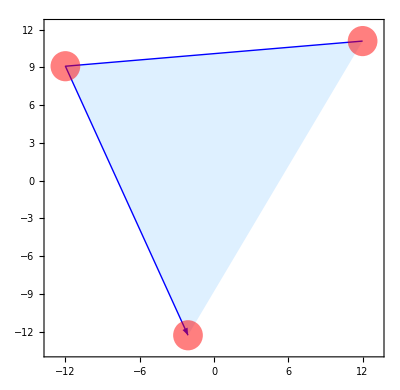

```mathematica
{p1,p2,p3}={{12.0,11.1},{-12.0,9.1},{-2.1,-12.3}};
r=1.2;
Graphics[{
{LightBlue,Polygon[{p1,p2,p3}]},
{Blue, Arrow[{p1,p2,p3}]},
{Opacity[0.5], Red,Disk[p1,r],Disk[p2,r],Disk[p3,r]}
},Frame->True]
```

I need to move each circle in along the line bisecting each angle until it is just inside the triangle.  At that point the circle is tangent to both edges!  I am going to add guide lines in the middle of each angle!  The easiest way to compute the bisectors is to compute the “incenter” of the triangle

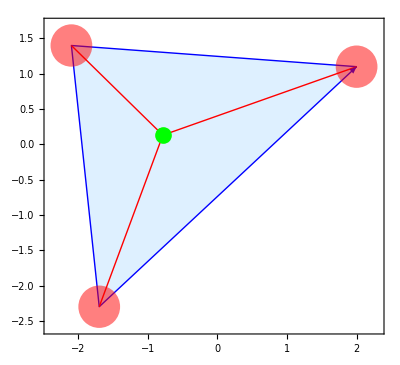

```mathematica
{p1,p2,p3}={{2.0,1.1},{-2.1,1.4},{-1.7,-2.3}};
r=0.3;
{a1,a2,a3}=Map[Norm,{p2-p3,p1-p3,p1-p2}];
pCenter=(a1 p1+a2 p2+a3 p3)/(a1+a2+a3);
Graphics[{
{LightBlue,Polygon[{p1,p2,p3}]},
{Blue, Arrow[{p1,p2,p3,p1}]},
{Red,Arrow[{p1,pCenter}],Arrow[{p2,pCenter}],Arrow[{p3,pCenter}] },
{PointSize[0.03],Green,Point[pCenter]},
{Opacity[0.5], Red,Disk[p1,r],Disk[p2,r],Disk[p3,r]}
},Frame->True]
```

Now we are going to do some simple trig (on the board) to work out how far to move each disk in!  We will check we did it correctly by computing the correct values of the shifts on the pic below.

{{1.34082,0.494264},{1.37266,0.528468},{1.3988,0.567203},{1.41862,0.609527},{1.43161,0.654415},{1.43748,0.700777},{1.43608,0.747488},{1.42744,0.793414},{1.41178,0.837442},{1.38946,0.878503},{1.36104,0.9156},{1.32721,0.947833},{1.28878,0.974421},{1.24668,0.994717},{1.20195,1.00823},{1.15566,1.01463},{1.10893,1.01377},{-0.876946,0.821586},{-0.900775,0.818311},{-0.924264,0.813138},{-0.947264,0.8061},{-0.969626,0.797242},{-0.991206,0.786621},{-1.01187,0.774305},{-1.03147,0.760374},{-1.0499,0.744917},{-1.06703,0.728033},{-1.08276,0.709831},{-1.09697,0.690428},{-1.10958,0.669949},{-1.12052,0.648525},{-1.1297,0.626294},{-1.13707,0.603399},{-1.14258,0.579987},{-1.52695,-1.40589},{-1.53223,-1.45252},{-1.53018,-1.4994},{-1.52085,-1.54538},{-1.50446,-1.58935},{-1.48142,-1.63022},{-1.45228,-1.667},{-1.41776,-1.69879},{-1.37871,-1.72481},{-1.33608,-1.74442},{-1.29091,-1.75714},{-1.24432,-1.76266},{-1.19743,-1.76085},{-1.1514,-1.75175},{-1.10734,-1.73558},{-1.06635,-1.71275},{-1.02943,-1.6838}}

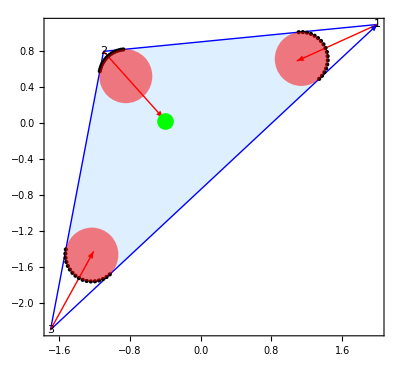

```mathematica
{p1,p2,p3}={{2.0,1.1},{-1.1,0.8},{-1.7,-2.3}};
r=0.3;
{a1,a2,a3}=Map[Norm,{p2-p3,p1-p3,p1-p2}];
pCenter=(a1 p1+a2 p2+a3 p3)/(a1+a2+a3);
(* make unit vectors towards in center *)
{τ1,τ2,τ3}= Map[Normalize,{pCenter-p1,pCenter-p2,pCenter-p3}];
(* make unit vectors pependicular to the τs *)
{n1,n2,n3}=Map[{-#⟦2⟧,#⟦1⟧}&,{τ1,τ2,τ3}];
{θ1,θ2,θ3}= {
0.5 ArcCos[((p2-p1).(p3-p1))/(Norm[p2-p1] Norm[p3-p1])],
0.5 ArcCos[((p3-p2).(p1-p2))/(Norm[p3-p2] Norm[p1-p2])],
0.5 ArcCos[((p2-p3).(p1-p3))/(Norm[p2-p3] Norm[p1-p3])]};

{d1,d2,d3}={r/Sin[θ1],r/Sin[θ2],r/Sin[θ3]};
(* Compute Complementary Angles *)
{θc1,θc2,θc3}={π/2-θ1,π/2-θ2,π/2-θ3};
(* Build Border Points *)
m=8;
BorderPoints=Join[
Table[ p1+τ1 d1 - r (τ1 Cos[θ]+n1 Sin[θ]),{θ,-θc1,θc1,θc1/m}],
Table[ p2+τ2 d2 - r (τ2 Cos[θ]+n2 Sin[θ]),{θ,-θc2,θc2,θc2/m}],
Table[ p3+τ3 d3 - r (τ3 Cos[θ]+n3 Sin[θ]),{θ,-θc3,θc3,θc3/m}]
]
(* Check that it works *)
Graphics[{
{LightBlue,Polygon[{p1,p2,p3}]},
{Blue, Arrow[{p1,p2,p3,p1}]},
{Red,Arrow[{p1,p1+τ1}],Arrow[{p2,p2+τ2}],Arrow[{p3,p3+τ3}] },
{PointSize[0.03],Green,Point[pCenter]},
{Black,Text["1",p1],Text["2",p2],Text["3",p3]},
{Black, Point[BorderPoints]},
{Opacity[0.5], Red,Disk[p1+d1 τ1,r],Disk[p2+d2 τ2,r],Disk[p3+d3 τ3,r]}
},Frame->True];
Graphics[{
{LightBlue,Polygon[BorderPoints]},
{Blue, Arrow[{p1,p2,p3,p1}]},
{Red,Arrow[{p1,p1+τ1}],Arrow[{p2,p2+τ2}],Arrow[{p3,p3+τ3}] },
{PointSize[0.03],Green,Point[pCenter]},
{Black,Text["1",p1],Text["2",p2],Text["3",p3]},
{Black, Point[BorderPoints]},
{Opacity[0.5], Red,Disk[p1+d1 τ1,r],Disk[p2+d2 τ2,r],Disk[p3+d3 τ3,r]}
},Frame->True]
```

## Semi Circle!

The semi circle is actually a slice off the top of a circle with the corners rounded off. 

It is defined by a big radius “R” a distance “d” up from the diameter and a rounding radius “r”.  It is easier (unless you love trig) to work out how far the disks need to move in now.

If we make up a recipe (or a thing to solve) we can work out what is “just-right”.

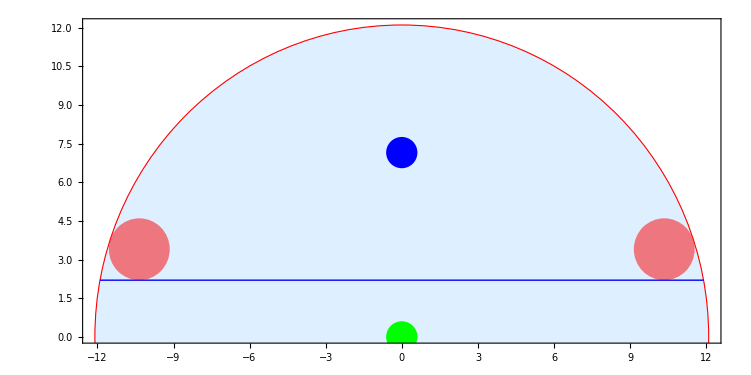

```mathematica
{R,d,r}={12.1,2.2,1.2};
x1=√(R^2-d^2);
s1=1.55;
Graphics[{
{LightBlue,EdgeForm[Red],Disk[{0,0},R]},
{Blue, Line[{{-x1,d},{x1,d}}]},
{PointSize[0.03],Green,Point[{0,0}]},
{PointSize[0.03],Blue,Point[{0,(R+d)/2}]},
{Opacity[0.5], Red,Disk[{-x1+s1,d+r},r],Disk[{x1-s1,d+r},r]}
},Frame->True,
PlotRange->{All,{0,R}}]
```

I need to find the value of the shift s when the big circle
	x^2+y^2=R^2
and the little circle radius r centered at {x1-s,d+r} 
	(x-(x1-s))^2+(y-(d+r))^2=r^2
are tangent. There are three unknowns x,y,and s: all the other things are inputs!  If I write
	f1[x,y]=x^2+y^2 and f2[x,y]=(x-(x1-s))^2+(y-(d+r))^2 
then the tangent condition (think back to Calcus III and Lagrange Multipliers) is
	∇f1[x,y]=λ∇f2[x,y] 
This is one vector equation with one more unknown λ. Writing this out as two scalar equations we have
	2x | = |  2λ(x-(x1-s))
2y | = | 2λ(y-(d+r))   
Putting this all together I have four scalar equations in the four unknowns x, y, s, and λ.  I should be able to get the computer to solve these.

```mathematica
Clear[R,r,x1,d,s,x,y]
x1=√(R^2-d^2);
FullSimplify[
s/.Solve[{
x^2+y^2==R^2,
(x-(x1-s))^2+(y-(d+r))^2==r^2,
2x == 2 λ (x-(x1-s)),
2y == 2 λ (y-(d+r))
},
{s,x,y,λ}
]
]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{((r-R) √(d+2 r-R) √(d+R))/(√(-(r-R)^2))+√(-d^2+R^2),(√(-(r-R)^2) √(d+2 r-R) √(d+R))/(r-R)+√(-d^2+R^2),(√(d-R) √(-(r+R)^2) √(d+2 r+R))/(r+R)+√(-d^2+R^2),(√(d-R) (r+R) √(d+2 r+R))/(√(-(r+R)^2))+√(-d^2+R^2)}

I know that d<R, r<R, and I need 0<s<R.  I am going to work out which is the appropriate solution.

```mathematica
TestsFuns[R_,r_,d_]:={((r-R) √(d+2 r-R) √(d+R))/(√(-(r-R)^2))+√(-d^2+R^2),(√(-(r-R)^2) √(d+2 r-R) √(d+R))/(r-R)+√(-d^2+R^2),(√(d-R) √(-(r+R)^2) √(d+2 r+R))/(r+R)+√(-d^2+R^2),(√(d-R) (r+R) √(d+2 r+R))/(√(-(r+R)^2))+√(-d^2+R^2)}
```

It looks as though the correct answer is the first one.

```mathematica
Chop[TestsFuns[12,1,0.2]]
```

{1.06398,22.9327,-0.946164,24.9428}

```mathematica
sHalfCircle[R_,r_,d_]:=((r-R) √(d+2 r-R) √(d+R))/(√(-(r-R)^2))+√(-d^2+R^2)
```

Lets check!  I think it looks good.

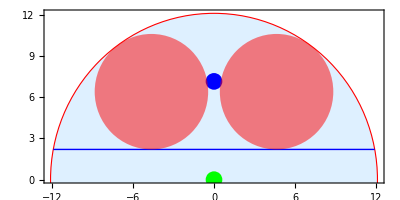

```mathematica
{R,d,r}={12.1,2.2,4.2};
x1=√(R^2-d^2);
s=sHalfCircle[R,r,d];
Graphics[{
{LightBlue,EdgeForm[Red],Disk[{0,0},R]},
{Blue, Line[{{-x1,d},{x1,d}}]},
{PointSize[0.03],Green,Point[{0,0}]},
{PointSize[0.03],Blue,Point[{0,(R+d)/2}]},
{Opacity[0.5], Red,Disk[{-x1+s,d+r},r],Disk[{x1-s,d+r},r]}
},Frame->True,
PlotRange->{All,{0,R}}]
```

All I have to do now is make the dots for the polygons.